```mathematica
hnew11=hnew11;
```

```mathematica
hh=Simplify[hnew11]
```

1/2 a (a J^2 p-2 a J^2 q+2 a II J (p-r)+a J^2 r+a II^2 (p+2 q+r)+(8 J δ)/R+4 II ν0+2 √(a (II-J)) √(a (II+J)) (J (k11-k12)+II (k11+k12)) Cos[α] Cos[Φ]+2 a f2 (II^2-J^2) Cos[2 Φ]-2 √(a (II-J)) √(a (II+J)) (J (k11-k12)+II (k11+k12)) Sin[α] Sin[Φ])

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]/.{α->0}
```

a (√(a (II-J)) √(a (II+J)) (J (k11-k12)+II (k11+k12)) Sin[Φ]+4 a f2 (II-J) (II+J) Cos[Φ] Sin[Φ])

```mathematica
Simplify[Solve[√(a (II-J)) √(a (II+J)) (J (k11-k12)+II (k11+k12)) Sin[Φ]+4 a f2 (II-J) (II+J) Cos[Φ] Sin[Φ]==0,Cos[Φ]]]
```

{{Cos[Φ]→-(a (J (k11-k12)+II (k11+k12)))/(4 f2 √(a (II-J)) √(a (II+J)))}}

```mathematica
Simplify[2(-(a (J (k11-k12)+II (k11+k12)))/(4 f2 √(a (II-J)) √(a (II+J))))^2 -1]
```

-1+(J (k11-k12)+II (k11+k12))^2/(8 f2^2 (II-J) (II+J))

```mathematica
Φshtrich=FullSimplify[D[hh,J]]/.{α->0}
```

a (a II (p-r)+a J (p-2 q+r)+(4 δ)/R+(a^2 ((II-2 J) (II+J) k11-(II-J) (II+2 J) k12) Cos[Φ])/(√(a (II-J)) √(a (II+J)))-2 a f2 J Cos[2 Φ])

```mathematica
Manipulate[ContourPlot[hh2/.{II->1,f2->.01, f1->2,R->1,p->3,r->0.06,δ->0,J->Cos[(x^2+y^2) π/2],Cos[Φ]->x/Sqrt[(x^2+y^2)],Cos[2 Φ]->2x^2/(x^2+y^2)-1,t->t1,λ->0.05},{x, -1,1},{y, -1, 1},Contours->30],{t1,-100,100}]
```

```mathematica
Manipulate[ContourPlot[hh2/.{II->1,f2->.01, f1->2,R->1,p->1,r->0.06,δ->0,J->-Cos[(x^2+y^2) π/2],Cos[Φ]->x/Sqrt[(x^2+y^2)],Cos[2 Φ]->2x^2/(x^2+y^2)-1,t->t1,λ->0.05},{x, -1,1},{y, -1, 1},Contours->30],{t1,-100,100}]
```

```mathematica
solJ=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-1,Cos[2Φ]->1},J]];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

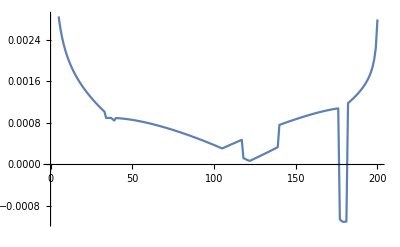

```mathematica
ListPlot[Table[δ/.Flatten[NSolve[{Φshtrich==0,Jshtrich==0}/.{II->1,f2->60,p->0,q->-0,r->0,k11->-20,k12->35,R->1/π,a->.0002,α->1},{δ,Φ}]][[7]],{J,-.999,.999,.01}],Joined->True]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-1,Cos[2Φ]->1},δ]];
sol1=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-(a (J (k11-k12)+II (k11+k12)))/(4 f2 √(a (II-J)) √(a (II+J))),Cos[2Φ]->-1+(J (k11-k12)+II (k11+k12))^2/(8 f2^2 (II-J) (II+J))},δ]];
```

```mathematica
soll=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->1,Cos[2Φ]->1},δ]];
```

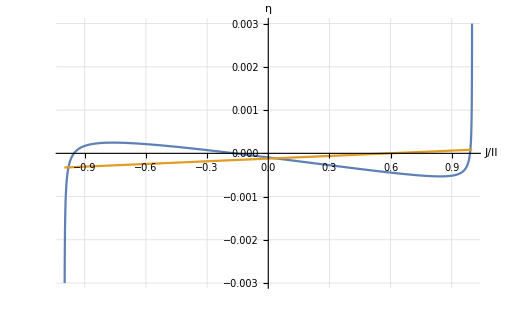

```mathematica
solPlot=sol/.{II->1,f2->-15, k11->-4,k12->-6,R->1/π,p->11,r->3,q->-1.5,a->.0002};
Jplot={δ/.{solPlot[[1]]}};

solPlot1=sol1/.{II->1,f2->-15, k11->-4,k12->-6,R->1/π,p->11,r->3,q->-1.5,a->.0002};
Jplot1={δ/.{solPlot1[[1]]}};

sollPlot=soll/.{II->1,f2->-15, k11->-4,k12->-6,R->1/π,p->11,r->3,q->-1.5,a->.0002};
Jplotl={δ/.{sollPlot[[1]]}(*,J/.{sollPlot[[2]]},J/.{sollPlot[[3]]},J/.{sollPlot[[4]]}*)};

Plot[{Jplot,Jplot1},{J,-1,1},PlotRange->{-.003,.003},LabelStyle->Directive[Black,16],AxesLabel->{"J/II","η"},GridLines->Automatic]
```

```mathematica
plotFase=Simplify[f1/(3 f2 √(ⅇ^(-4 t λ) (II^2-J^2)))/.{J->(-3 II p R+3 II r R-32 ⅇ^(2 t λ) δ)/(3 (2 f2+p+r) R)}]
```

f1/(3 f2 √(ⅇ^(-4 t λ) (II^2-((3 II (p-r) R+32 ⅇ^(2 t λ) δ)^2)/(9 (2 f2+p+r)^2 R^2))))

```mathematica
Manipulate[Plot[plotFase/.{II->1,f2->.02, f1->1,R->1,p->0.3,r->0.06,t->f1a,λ->0.05},{δ,-1,1},PlotRange->{-1,1}],{f1a,-100,100}]
```

```mathematica
Solve[δ==-3/32 ⅇ^(-2 t λ) (2 f2 J+II p+J p-II r+J r) R,J]
```

{{J→(-3 II p R+3 II r R-32 ⅇ^(2 t λ) δ)/(3 (2 f2+p+r) R)}}

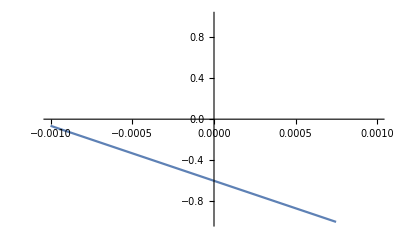

```mathematica
Plot[(26.666666666666664 ⅇ^(0.1 t) (-0.0225 ⅇ^(-0.1 t)-1. δ))/.{t->30},{δ,-0.001,0.001},PlotRange->1]
```

```mathematica
Jplot/.{δ->-0.7}
```

{-0.998867-2.06595×10^-19 ⅈ,0.536878+1.34627×10^-17 ⅈ,0.649347-1.67795×10^-17 ⅈ,0.982453+3.52331×10^-18 ⅈ}

```mathematica
plotFase=-f/(2 f1 √(II^2-J^2))/.{J->(-II p R+II r R-4 δ)/((p-2 q+r) R)};
```

```mathematica
Manipulate[Plot[plotFase/.{II->1,f->0.2, f1->f1a,R->1,p->0.3,q->-.2,r->0.6},{δ,-1,1},PlotRange->{-1,1}],{f1a,0.01,1}]
```

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→-0.943957-9.33782×10^-19 ⅈ,J→0.142438+1.47905×10^-17 ⅈ,J→0.348935-1.75238×10^-17 ⅈ,J→0.852584+3.66707×10^-18 ⅈ}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→-0.860094,J→0.834837,J→16.0126-10.0061 ⅈ,J→16.0126+10.0061 ⅈ}

```mathematica
ΦΦ=FullSimplify[D[hh,{Φ,2}]]
```

1/2 (-f1 √((II-J) (II+J)) Cos[Φ]+3 f2 (II-J) (II+J) Cos[2 Φ])

```mathematica
JJ = FullSimplify[D[hh,{J,2}]]
```

1/8 (-(4 f1 II^2 Cos[Φ])/((II-J) (II+J))^(3/2)+3 (4 f2+p+r+2 f2 Cos[2 Φ]))

```mathematica
(J/.{J0})/.{II->1}
```

Indeterminate

```mathematica
(J/.solJ[[3]])/.{f2->-.1, f1->.1,R->1,p->-.3,r->-.1,δ->-0.02,II->0.3}
```

-0.112648

Piecewise[{{(8.35758×10^-6-1.55672×10^-14 ⅈ)+(1.99455×10^-14-2.34688×10^-22 ⅈ) √II+(1.0447×10^-6+1.9459×10^-15 ⅈ) II+(1437.22-0.000016911 ⅈ) II^(3/2)+(8.62182×10^19+8.0297×10^11 ⅈ) II^2+O[II]^(5/2), Im[-1.32478×10^-25 √II-6.93889×10^-18 II-9.54606×10^-9 II^(3/2)+1.56098 II^2]≥0}, {(8.35758×10^-6+1.55672×10^-14 ⅈ)+(1.99455×10^-14+2.34688×10^-22 ⅈ) √II+(1.0447×10^-6-1.9459×10^-15 ⅈ) II+(1437.22+0.000016911 ⅈ) II^(3/2)+(8.62182×10^19-8.0297×10^11 ⅈ) II^2+O[II]^(5/2), True}}]

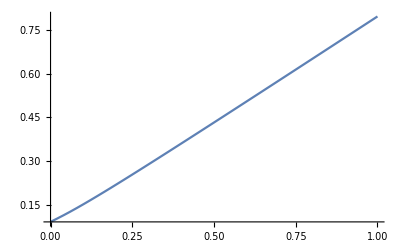

0.218004

```mathematica
w=Simplify[Sqrt[2ΦΦ JJ]/.{Cos[Φ]->1,Cos[2Φ]->1}];
Simplify[Series[(w/.solJ[[4]])/.{f2->-.1, f1->.1,R->1,p->-.3,r->-.1,δ->-0.02},{II,0,2}]]
J0=solJ[[4]]/.{f2->-.1, f1->.1,R->1,p->-.3,r->-.1,δ->-0.02};
Plot[Re[(w/.{J0})/.{f2->-.1, f1->.1,R->1,p->-.3,r->-.1,δ->-0.02}],{II,0,1},PlotRange->All]
(w/.solJ[[4]])/.{f2->-.1, f1->.1,R->1,p->-.3,r->-.1,δ->-0.02,II->.2}
```

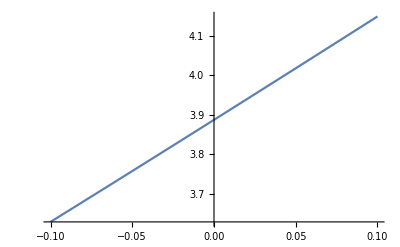

```mathematica
w=Simplify[Sqrt[2ΦΦ JJ]/.{Cos[Φ]->-1,Cos[2Φ]->1}];
J0=solJ[[4]]/.{II->1,f2->.1, f1->2,R->1,p->3,r->1};
Plot[(w/.{J0})/.{II->1,f2->.1, f1->2,R->1,p->3,r->1},{δ,-0.1,0.1},PlotRange->All]
```

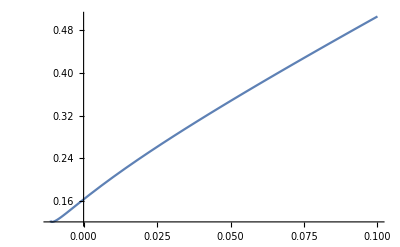

```mathematica
w=Simplify[Sqrt[2ΦΦ JJ]/.{Cos[Φ]->1,Cos[2Φ]->1}];
J0=solJ[[4]]/.{II->.1,f2->2, f1->-.02,R->1,p->-5.5,r->-6};
Plot[(w/.{J0})/.{II->.1,f2->2, f1->-.02,R->1,p->-5.5,r->-6},{δ,-0.1,0.1},PlotRange->All]
```

```mathematica
Jnew=(J/.{J0})+d J;
```

```mathematica
Simplify[Series[hh/.{J->Jnew,Cos[Φ]->-1+.5(d Φ)^2,Cos[2Φ]->1-.5(2d Φ)^2,II->1,f2->-1, f1->1,R->1,p->1,r->2,δ->0.01},{d,0,2}]]
```

-0.251364+(6.2076 J^2+0.0000824894 Φ^2) d^2+O[d]^3

```mathematica
Sqrt[0.00008248941885935501/6.207604638486918 ]
```

0.00364533

```mathematica
ΦJ=FullSimplify[D[D[hh,Φ],J]]
```

-(f J Sin[Φ])/(2 √((II-J) (II+J)))-f1 J Sin[2 Φ]

```mathematica
ΦΦ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0756148

```mathematica
JJ/.{Φ->π,sol1[[4]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.241302

```mathematica
ΦΦ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.0550497

```mathematica
JJ/.{Φ->π,sol2[[2]],II->1,f->-0.2,δ->0.09,R->1,p->-0.02,q->-0.02,r->0.02}
```

0.609426

```mathematica
Jstrd=Jshtrich/.{J->J[t],Φ->Φ[t]};
Φstrd=Φshtrich/.{J->J[t],Φ->Φ[t]};
```

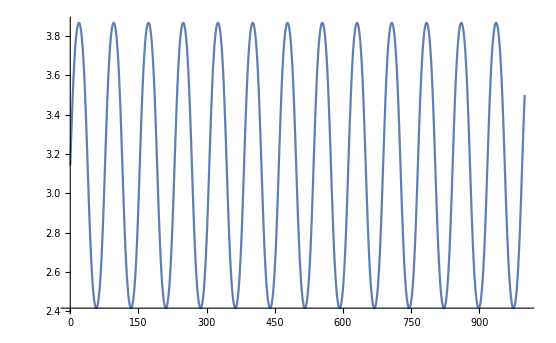

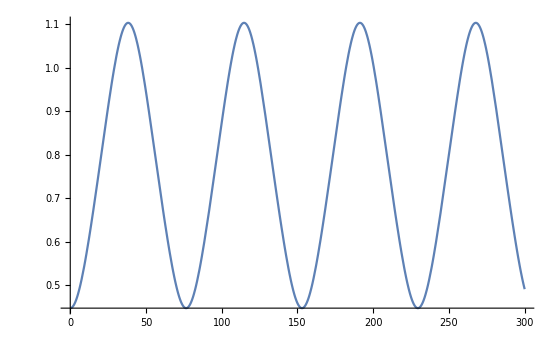

0.000358748

```mathematica
s=Flatten[NDSolve[{J'[t]==Jstrd,Φ'[t]==Φstrd,J[0]==0.8,Φ[0]==π}/.{f2->.061, f1->0,R->1,p->0,r->0,δ->-0.02,II->1},{J[t],Φ[t]},{t,0,1000}]];
Plot[(Φ[t]/.s),{t,0, 1000}]
b=Plot[Sqrt[-(J[t]/.s)+1],{t,0, 300}]
(((Φ[t]/.s)/.{t->1000})-(((Φ[t]/.s)/.{t->0})))/1000
```

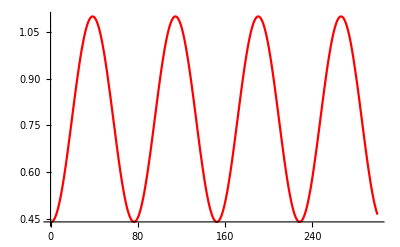

```mathematica
a=Plot[0.33Cos[2 π x/76+π-0.05]+0.77,{x,0,300},PlotStyle->Red]
```

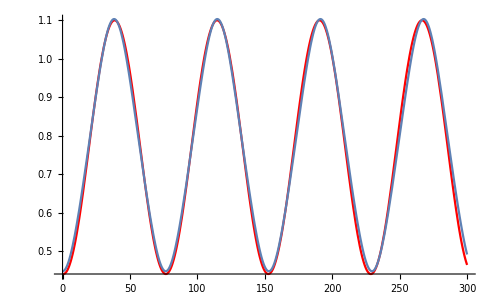

```mathematica
Show[{a,b}]
```

```mathematica
Plot[Cos[x]^2,{x,0,100},PlotStyle->Red]
```

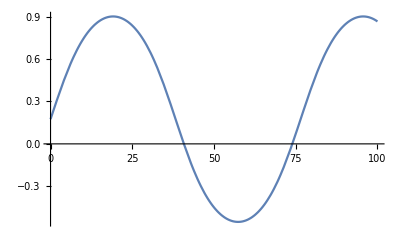

```mathematica
d=Plot[(Φ[t]/.s)-(2.967-0t),{t,0, 100}]
```

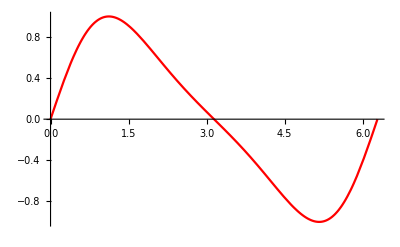

```mathematica
Plot[Sin[x+0.5Sin[x]],{x,0,2π},PlotStyle->Red]
```

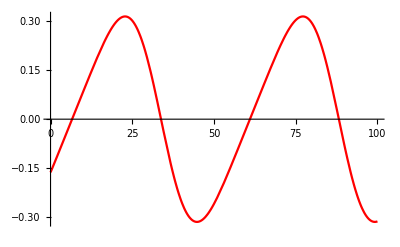

```mathematica
c=Plot[-.315Sin[2π/54.4 x+2.38+0.315Sin[2π/54.4 x+2.38]],{x,0,100},PlotStyle->Red]
```

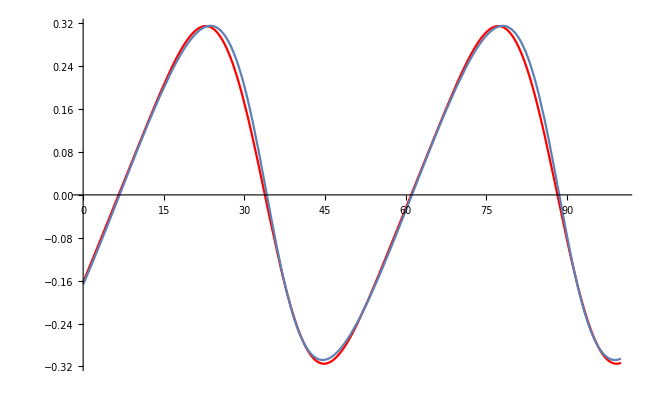

```mathematica
Show[c,d]
```

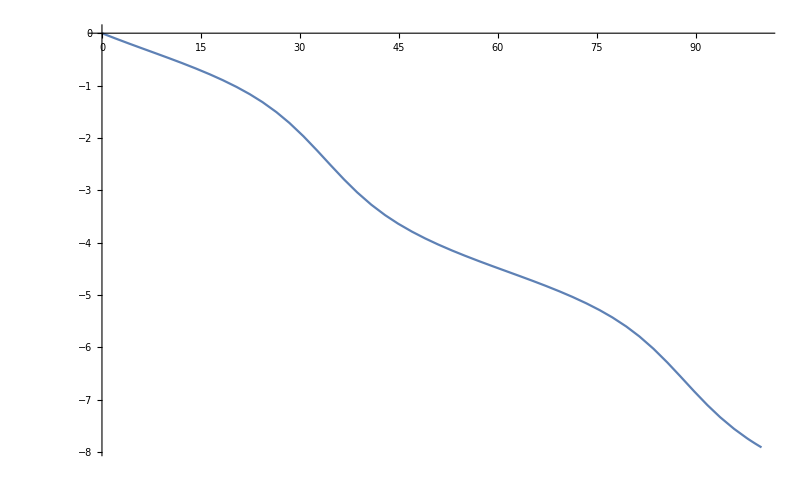

```mathematica
ϕsumsolve=NDSolve[{ϕsum'[t]==ϕsumstr/.{f2->.061, f1->0,R->1,p->0,r->0,δ->-0.02,II->1,J->1-(0.161Cos[2 π t/54.3+π-0.8]+1.075)^2,Φ->1.967-0.05779t-.315Sin[2π/54.4 t+2.38+0.315Sin[2π/54.4t+2.38]]},ϕsum[0]==0},ϕsum[t],{t,0,1000}];
Plot[ϕsum[t]/.Flatten[ϕsumsolve],{t,0,100}]
```

```mathematica
Φ->(Φ0+ν t)+C1 Sin[t-t0+C1 Sin[t-t0]];
```

```mathematica
((Φ[t]/.s)/.{t->100})/100
```

-1.46422+0. ⅈ

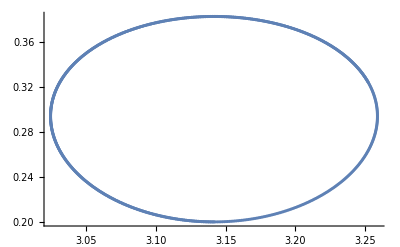

```mathematica
a=ListPlot[Table[{Φ[t],J[t]}/.s,{t,0,100,.1}]]
```

```mathematica
}
```

```mathematica
Manipulate[Manipulate[ContourPlot[hh/.{f2->f21, f1->0,R->1,p->0,r->0,δ->δ1,II->.5,t->0,λ->0.05},{Φ, - π,π},{J, -.5,.5},Contours->30],{δ1,-.1,.1}],{f21,-.2,.2}]
```

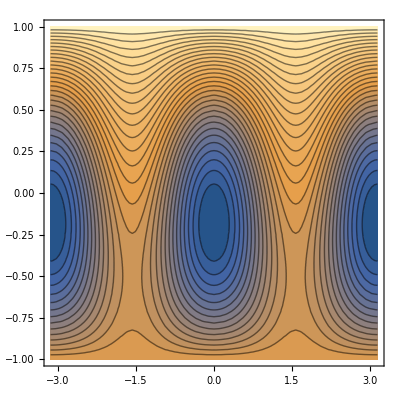

```mathematica
b=ContourPlot[hh/.{f2->1, f1->0,R->1,p->0,r->0,δ->0.2,II->1},{Φ, - π,π},{J, -1,1},Contours->30]
```

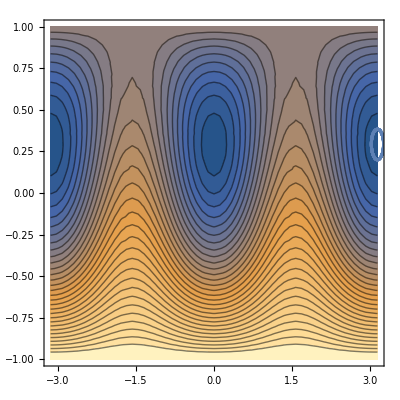

```mathematica
Show[{b,a}]
```

```mathematica
Astr=Simplify[(Jstrd/.{J[t]->A[t]A[t],f1->0,p->0,r->0})/(2 A[t]),Assumptions->{A[t]>0}]
Φstr=Φstrd/.{f1->0,p->0,r->0,J[t]->A[t]A[t]}
```

(3 f2 (-II^2+A[t]^4) Sin[2 Φ[t]])/(8 A[t])

1/8 ((16 δ)/R+6 f2 A[t]^2+12 f2 A[t]^2 Cos[Φ[t]]^2)

```mathematica
Simplify[{Astr,Φstr}/.{Φ[t]->(Φ0+ν t)+C1 Sin[t-t0+C1 Sin[t-t0]]}]
```

{(3 f2 (-II^2+A[t]^4) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])/(8 A[t]),(2 δ)/R+3/4 f2 A[t]^2 (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])}

```mathematica
Simplify[D[(Φ0+ν t)+C1 Sin[t-t0+C1 Sin[t-t0]],t]]
```

ν+C1 (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]

```mathematica
Simplify[{A'[t]==(3 f2 (-II^2+A[t]^4) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])/(8 A[t]),ν+C1 (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]==(2 δ)/R+3/4 f2 A[t]^2 (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])}]
```

{A'[t]==(3 f2 (-II^2+A[t]^4) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])/(8 A[t]),4 (-(2 δ)/R+ν+C1 (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]])==3 f2 A[t]^2 (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])}

```mathematica
Solve[4 (-(2 δ)/R+ν+C1 (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]])==3 f2 A[t]^2 (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]),A[t]]
```

{{A[t]→-(2 √(-2 δ+R ν+C1 R Cos[t-t0+C1 Sin[t-t0]]+C1^2 R Cos[t-t0] Cos[t-t0+C1 Sin[t-t0]]))/(√3 √(2 f2 R+f2 R Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))},{A[t]→(2 √(-2 δ+R ν+C1 R Cos[t-t0+C1 Sin[t-t0]]+C1^2 R Cos[t-t0] Cos[t-t0+C1 Sin[t-t0]]))/(√3 √(2 f2 R+f2 R Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))}}

```mathematica
Simplify[(A'[t]==(3 f2 (-II^2+A[t]^4) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])/(8 A[t]))/.{A[t]->(2 √(-2 δ+R ν+C1 R Cos[t-t0+C1 Sin[t-t0]]+C1^2 R Cos[t-t0] Cos[t-t0+C1 Sin[t-t0]]))/(√3 √(2 f2 R+f2 R Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))}]
```

A'[t]==(3 √3 f2 √(f2 R (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])) (-II^2+(16 (-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]])^2)/(9 f2^2 R^2 (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])^2)) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])/(16 √(-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]))

```mathematica
Simplify[D[(2 √(-2 δ+R ν+C1 R Cos[t-t0+C1 Sin[t-t0]]+C1^2 R Cos[t-t0] Cos[t-t0+C1 Sin[t-t0]]))/(√3 √(2 f2 R+f2 R Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])),t]]
```

(f2 R (C1 R (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]) (-C1 Cos[t-t0+C1 Sin[t-t0]] Sin[t-t0]-(1+C1 Cos[t-t0])^2 Sin[t-t0+C1 Sin[t-t0]])+2 (ν+C1 (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]) (-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))/(√3 √(-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]) (f2 R (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))^(3/2))

```mathematica
Simplify[(f2 R (C1 R (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]) (-C1 Cos[t-t0+C1 Sin[t-t0]] Sin[t-t0]-(1+C1 Cos[t-t0])^2 Sin[t-t0+C1 Sin[t-t0]])+2 (ν+C1 (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]) (-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))/(√3 √(-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]) (f2 R (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])]))^(3/2))==(3 √3 f2 √(f2 R (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])) (-II^2+(16 (-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]])^2)/(9 f2^2 R^2 (2+Cos[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])^2)) Sin[2 (t ν+Φ0+C1 Sin[t-t0+C1 Sin[t-t0]])])/(16 √(-2 δ+R ν+C1 R (1+C1 Cos[t-t0]) Cos[t-t0+C1 Sin[t-t0]]))]
```

$Aborted

```mathematica
Simplify[FullSimplify[(Astr+I A[t]Φstr)/.{f1->0,p->0,r->0,s->t,R->1},Assumptions->{δ>0,Φ[t]>0,A[t]>0}]/.{Φ[t]->-I Log[A[t]/Abs[A[t]]],A[t]->Abs[A[t]]}]
```

(ⅈ ((16 δ+3/2 f2 A[t]^2) Abs[A[t]]^2+12 f2 Abs[A[t]]^4+(9 f2 Abs[A[t]]^6)/(2 A[t]^2)+3 f2 II^2 Sinh[2 Log[A[t]/Abs[A[t]]]]))/(8 Abs[A[t]])

```mathematica
eqA=Simplify[D[A[t]/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t]},t]==(ⅈ ((16 δ+3/2 f2 A[t]^2) Abs[A[t]]^2+12 f2 Abs[A[t]]^4+(9 f2 Abs[A[t]]^6)/(2 A[t]^2)+3 f2 II^2 Sinh[2 Log[A[t]/Abs[A[t]]]]))/(8 Abs[A[t]]^2)A[t]/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t]}, Assumptions->{t>0}]
```

ⅈ (C1 ⅇ^(ⅈ t ν1) ν1+C2 ⅇ^(ⅈ t ν2) ν2)==1/(8 Abs[C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)]^2)ⅈ (C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)) ((3/2 (C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2))^2 f2+16 δ) Abs[C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)]^2+12 f2 Abs[C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)]^4+(9 f2 Abs[C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)]^6)/(2 (C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2))^2)+3 f2 II^2 Sinh[2 Log[(C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2))/Abs[C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)]]])

```mathematica
Solve[Simplify[eqA/.{t->0}],C2]
```

{{C2→-C1-(2^(1/3) (216 f2 δ-108 f2 ν2))/(27 f2 (8748 C1 f2^2 ν1-8748 C1 f2^2 ν2+√(4 (216 f2 δ-108 f2 ν2)^3+(8748 C1 f2^2 ν1-8748 C1 f2^2 ν2)^2))^(1/3))+((8748 C1 f2^2 ν1-8748 C1 f2^2 ν2+√(4 (216 f2 δ-108 f2 ν2)^3+(8748 C1 f2^2 ν1-8748 C1 f2^2 ν2)^2))^(1/3))/(27 2^(1/3) f2)},{C2→-C1+((1+ⅈ √3) (216 f2 δ-108 f2 ν2))/(27 2^(2/3) f2 (8748 C1 f2^2 ν1-8748 C1 f2^2 ν2+√(4 (216 f2 δ-108 f2 ν2)^3+(8748 C1 f2^2 ν1-8748 C1 f2^2 ν2)^2))^(1/3))-((1-ⅈ √3) (8748 C1 f2^2 ν1-8748 C1 f2^2 ν2+√(4 (216 f2 δ-108 f2 ν2)^3+(8748 C1 f2^2 ν1-8748 C1 f2^2 ν2)^2))^(1/3))/(54 2^(1/3) f2)},{C2→-C1+((1-ⅈ √3) (216 f2 δ-108 f2 ν2))/(27 2^(2/3) f2 (8748 C1 f2^2 ν1-8748 C1 f2^2 ν2+√(4 (216 f2 δ-108 f2 ν2)^3+(8748 C1 f2^2 ν1-8748 C1 f2^2 ν2)^2))^(1/3))-((1+ⅈ √3) (8748 C1 f2^2 ν1-8748 C1 f2^2 ν2+√(4 (216 f2 δ-108 f2 ν2)^3+(8748 C1 f2^2 ν1-8748 C1 f2^2 ν2)^2))^(1/3))/(54 2^(1/3) f2)}}

```mathematica
Jstrd=Jstrd/.{f2->.1,f1->0,p->0,r->0,II->1,R->1,δ->0};
Φstrd=Φstrd/.{f2->.1,f1->0,p->0,r->0,II->1,R->1,δ->0};
```

```mathematica
Simplify[D[2(a1 Sin[w t+α]+b1)^2+1,t]==Jstrd/.{J[t]->2(a1 Sin[w t+α]+b1)^2+1}]
```

4 a1 w Cos[t w+α] (b1+a1 Sin[t w+α])==0.075 (-1+(1+2 (b1+a1 Sin[t w+α])^2)^2) Sin[2 Φ[t]]

```mathematica
Simplify[D[2Φ[t],t]==2Φstrd/.{J[t]->2(a1 Sin[w t+α]+b1)^2+1}]
```

2 Φ'[t]==(0.15+0.3 Cos[Φ[t]]^2) (1+2 (b1+a1 Sin[t w+α])^2)

```mathematica
sin=(4 a1 w Cos[t w+α] (b1+a1 Sin[t w+α])/(0.075(-1+(1+2 (b1+a1 Sin[t w+α])^2)^2)));
Simplify[D[sin,t]/Sqrt[1-sin^2]==0.15(2+Sqrt[1-sin^2]) (1+2 (b1+a1 Sin[t w+α])^2)]/.{t->0}
```

(6.66667 a1 w^2 (-2. a1-1.5 a1^3-6. a1 b1^2+1. a1^3 Cos[2 α]+0.5 a1^3 Cos[4 α]-2. b1 Sin[α]-7.5 a1^2 b1 Sin[α]-2. b1^3 Sin[α]-1.5 a1^2 b1 Sin[3 α]))/((b1+a1 Sin[α])^2 (1.+b1^2+2. a1 b1 Sin[α]+a1^2 Sin[α]^2)^2 √(1-(2844.44 a1^2 w^2 Cos[α]^2 (b1+a1 Sin[α])^2)/((-1+(1+2 (b1+a1 Sin[α])^2)^2)^2)))==0.15 (1+2 (b1+a1 Sin[α])^2) (2+√(1-(2844.44 a1^2 w^2 Cos[α]^2 (b1+a1 Sin[α])^2)/((-1+(1+2 (b1+a1 Sin[α])^2)^2)^2)))

```mathematica
DSolve[ρ'[x](2-Cos[x])==3/2ρ[x]^2 Sin[x]-a Sin[x](2-Cos[x])^2+b Sin[x],ρ[x],x]
```

{{ρ[x]→(2 (-2+Cos[x]) Csc[x] (1/2 ⅈ √(3/2) √a (BesselY[-1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]-BesselY[1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]) Sin[x]+1/2 ⅈ √(3/2) √a (BesselJ[-1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]-BesselJ[1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]) C[1] Sin[x]))/(3 (BesselY[ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]+BesselJ[ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]] C[1]))}}

```mathematica
Integrate[(2 (-2+Cos[x]) Csc[x] (1/2 ⅈ √(3/2) √a (BesselY[-1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]-BesselY[1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]) Sin[x]+1/2 ⅈ √(3/2) √a (BesselJ[-1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]-BesselJ[1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]) C[1] Sin[x]))/(3 (BesselY[ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]+BesselJ[ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]] C[1])),x]
```

2/3 ∫(((-2+Cos[x]) Csc[x] (1/2 ⅈ √(3/2) √a (BesselY[-1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]-BesselY[1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]) Sin[x]+1/2 ⅈ √(3/2) √a (BesselJ[-1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]-BesselJ[1+ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]) C[1] Sin[x]))/(BesselY[ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]]+BesselJ[ⅈ √(3/2) √b,ⅈ √6 √a-ⅈ √(3/2) √a Cos[x]] C[1]))ⅆx

```mathematica
Simplify[{2Φ'[t]==2Φstrd/.{f2->.1,f1->0,p->0,r->0,II->1,R->1,δ->0},J'[t]==Jstrd/.{f2->.1,f1->0,p->0,r->0,II->1,R->1,δ->0}}]
```

{2 Φ'[t]==(0.15+0.3 Cos[Φ[t]]^2) J[t],J'[t]==0.075 (-1.+J[t]^2) Sin[2 Φ[t]]}

```mathematica
Simplify[2Jstrd/J[t]+ 2I Φstrd]
```

(0.+0.3 ⅈ) (0.5+1. Cos[Φ[t]]^2) J[t]+(0.15 (-1.+J[t]^2) Sin[2 Φ[t]])/J[t]

```mathematica
DSolve[{Φ'[t]==Φstrd/.{f2->.1,f1->0,p->0,r->0,II->1,R->1,δ->0},J'[t]==Jstrd/.{f2->.1,f1->0,p->0,r->0,II->1,R->1,δ->0}},{Φ[t],J[t]},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

```mathematica
FullSimplify[(J''+4 J^2 (J')^4/(J^2-II^2)^2-4J'' J (J')^2/(J^2-II^2))16/(9 f2^2 (J^2-II^2))+9/4f2^2 J^2 (1-(4J'/(3f2(J^2-II^2)))^2)^2-4J(1-(4J'/(3f2(J^2-II^2)))^2)(J''-2J(J')^2/(J^2-II^2))/(J^2-II^2)-(4δ+3f2 J)^2(1-(4J'/(3f2(J^2-II^2)))^2)]
```

1/(36 f2^2 (II-J)^4 (II+J)^4)(256 J^2 (-1-II^2+J^2) (J')^4+(II-J)^3 (II+J)^3 (-9 f2^2 (II-J) (II+J) (3 f2 J+8 δ) (9 f2 J+8 δ)+16 (-4+9 f2^2 J) J'')+64 (II-J) (II+J) (J')^2 ((II-J) (II+J) (3 f2 J+4 δ)^2+4 J (-1-II^2+J^2) J''))

```mathematica
DSolve[(256 J^2 (-1-II^2+J^2) (J')^4+(II-J)^3 (II+J)^3 (-9 f2^2 (II-J) (II+J) (3 f2 J+8 δ) (9 f2 J+8 δ)+16 (-4+9 f2^2 J) J'')+64 (II-J) (II+J) (J')^2 ((II-J) (II+J) (3 f2 J+4 δ)^2+4 J (-1-II^2+J^2) J'')/.{J->J[t],J'->D[J[t],t],J''->D[J[t],{t,2}],II->1,f2->0.1})==0,J[t],t]
```

```mathematica
Normal[256 J[t]^2 (-2+J[t]^2) J'[t]^4+(1-J[t])^3 (1+J[t])^3 (-0.09000000000000002 (1-J[t]) (8 δ+0.30000000000000004 J[t]) (8 δ+0.9 J[t]) (1+J[t])+16 (-4+0.09000000000000002 J[t]) J''[t])+64 (1-J[t]) (1+J[t]) J'[t]^2 ((1-J[t]) (4 δ+0.30000000000000004 J[t])^2 (1+J[t])+4 J[t] (-2+J[t]^2) J''[t])]
```

256 J[t]^2 (-2+J[t]^2) J'[t]^4+(1-J[t])^3 (1+J[t])^3 (-0.09 (1-J[t]) (8 δ+0.3 J[t]) (8 δ+0.9 J[t]) (1+J[t])+16 (-4+0.09 J[t]) J''[t])+64 (1-J[t]) (1+J[t]) J'[t]^2 ((1-J[t]) (4 δ+0.3 J[t])^2 (1+J[t])+4 J[t] (-2+J[t]^2) J''[t])

```mathematica
%23[[1]]/.{f2->-.1, f1->0,R->1,p->0,r->0,δ->-0.02,II->1}
%23[[2]]/.{f2->-.1, f1->0,R->1,p->0,r->0,δ->-0.02,II->1}
```

$Aborted

```mathematica
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
Astr=Simplify[(Jxstrd/.{Jx[t]->A[t]A[t],Jy[t]->B[t]B[t]})/(2 A[t]),Assumptions->{A[t]>0,B[t]>0}]
Bstr=Simplify[(Jystrd/.{Jx[t]->A[t]A[t],Jy[t]->B[t]B[t]})/(2B[t]),Assumptions->{A[t]>0,B[t]>0}]
```

-1/4 B[t] (-f1+6 f2 A[t] B[t] Cos[(2 s δ)/R+ϕx[t]-ϕy[t]]) Sin[(2 s δ)/R+ϕx[t]-ϕy[t]]

1/4 A[t] (-f1+6 f2 A[t] B[t] Cos[(2 s δ)/R+ϕx[t]-ϕy[t]]) Sin[(2 s δ)/R+ϕx[t]-ϕy[t]]

```mathematica
Astr/.{f1->0,p->0,r->0,s->t}
Bstr/.{f1->0,p->0,r->0,s->t}
ϕastr=Simplify[(ϕxstrd/.{f1->0,p->0,r->0,s->t})/.{Jx[t]->A[t]A[t],Jy[t]->B[t]B[t]},Assumptions->{A[t]>0,B[t]>0}]
ϕbstr=Simplify[(ϕystrd/.{f1->0,p->0,r->0,s->t})/.{Jx[t]->A[t]A[t],Jy[t]->B[t]B[t]},Assumptions->{A[t]>0,B[t]>0}]
```

-3/2 f2 A[t] B[t]^2 Cos[(2 t δ)/R+ϕx[t]-ϕy[t]] Sin[(2 t δ)/R+ϕx[t]-ϕy[t]]

3/2 f2 A[t]^2 B[t] Cos[(2 t δ)/R+ϕx[t]-ϕy[t]] Sin[(2 t δ)/R+ϕx[t]-ϕy[t]]

-3/4 f2 B[t]^2 (2+Cos[(4 t δ)/R+2 ϕx[t]-2 ϕy[t]])

-3/4 f2 A[t]^2 (2+Cos[(4 t δ)/R+2 ϕx[t]-2 ϕy[t]])

```mathematica
FullSimplify[(Astr+I A[t] ϕastr)/.{f1->0,p->0,r->0,s->t},Assumptions->{δ>0,t>0,R>0,ϕx[t]>0,ϕy[t]>0}]
```

-3/4 ⅈ (2+ⅇ^(-(2 ⅈ (2 t δ+R ϕx[t]-R ϕy[t]))/R)) f2 A[t] B[t]^2

```mathematica
FullSimplify[(Bstr+I B[t] ϕbstr)/.{f1->0,p->0,r->0,s->t},Assumptions->{δ>0,t>0,R>0,ϕx[t]>0,ϕy[t]>0}]
```

-3/4 ⅈ ⅇ^(-2 ⅈ ϕy[t]) (ⅇ^(2 ⅈ ((2 t δ)/R+ϕx[t]))+2 ⅇ^(2 ⅈ ϕy[t])) f2 A[t]^2 B[t]

```mathematica
{ A'[t]==Simplify[Simplify[-3/4 ⅈ (2+ⅇ^(-(2 ⅈ (2 t δ+R ϕx[t]-R ϕy[t]))/R)) f2 A[t] B[t]^2 Exp[I ϕx[t]]Exp[-I ϕx[t]]Exp[-2I ϕy[t]]]/.{ ϕx[t]->-I Log[A[t]/Abs[A[t]]], ϕy[t]->-I Log[B[t]/Abs[B[t]]]}], B'[t]==Simplify[Simplify[-3/4 ⅈ ⅇ^(-2 ⅈ ϕy[t]) (ⅇ^(2 ⅈ ((2 t δ)/R+ϕx[t]))+2 ⅇ^(2 ⅈ ϕy[t])) f2 A[t]^2 B[t]Exp[I ϕy[t]]Exp[-2I ϕx[t]]Exp[-I ϕy[t]]]/.{ ϕx[t]->-I Log[A[t]/Abs[A[t]]], ϕy[t]->-I Log[B[t]/Abs[B[t]]]}]}/.{f1->0,p->0,r->0,s->t}
```

{A'[t]==-(3 ⅈ f2 (2 A[t]^2 Abs[B[t]]^2+ⅇ^(-(4 ⅈ t δ)/R) Abs[A[t]]^2 B[t]^2))/(4 A[t]),B'[t]==-(3 ⅈ f2 (ⅇ^((4 ⅈ t δ)/R) A[t]^2 Abs[B[t]]^2+2 Abs[A[t]]^2 B[t]^2))/(4 B[t])}

```mathematica
ν[A^2]
```

```mathematica
eqABf2=Simplify[{D[A[t]/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t]},t]==-(3 ⅈ f2 (2 A[t]^2 Abs[B[t]]^2+ⅇ^(-(4 ⅈ t δ)/R) Abs[A[t]]^2 B[t]^2))/(4 A[t])/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t],B[t]->C3 Exp[I ν3 t]+C4 Exp[I ν4 t]},D[B[t]/.{B[t]->C3 Exp[I ν3 t]+C4 Exp[I ν4 t]},t]==-(3 ⅈ f2 (ⅇ^((4 ⅈ t δ)/R) A[t]^2 Abs[B[t]]^2+2 Abs[A[t]]^2 B[t]^2))/(4 B[t])/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t],B[t]->C3 Exp[I ν3 t]+C4 Exp[I ν4 t]}}, Assumptions->{t>0}];
```

```mathematica
Simplify[Solve[Simplify[eqABf2/.{t->0}],{C3,C4}]]
```

{{C3→(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),C4→-(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2)))},{C3→-(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),C4→(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2)))}}

```mathematica
Simplify[Series[Simplify[(eqABf2/.{C3->(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),C4->-(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),R->1})/.{C2->0},Assumptions->{t>0,C1>0,C2>0}]/.{C2->0},{t,0,1}]/.{t->0},Assumptions->{t>0}]
```

{C1 (ν1+f2 Abs[(√ν1 (ν3-ν4))/(√f2 √((ν3-ν4)^2))]^2)==0,(C1 √f2 (ν3-ν4) (ν1+f2 Abs[(√ν1 (ν3-ν4))/(√f2 √((ν3-ν4)^2))]^2))/(√ν1 √((ν3-ν4)^2))==0}

```mathematica
Simplify[Series[Simplify[(eqABf2/.{C3->(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),C4->-(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),R->1})/.{C2->0},Assumptions->{t>0,C1>0,C2>0}]/.{C2->0},{t,0,1}],Assumptions->{t>0}]
```

{Abs[(√ν1 (9 C1^2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2-4 ⅇ^(ⅈ t ν4) ν3+4 ⅇ^(ⅈ t ν3) ν4))/(√f2 √((ν3-ν4)^2))]^2 ((C1 f2)/6+1/6 ⅈ C1 f2 (4 δ+ν1) t+O[t]^2)+((8 C1 ν1)/3+2/3 C1 ν1 (9 ⅈ C1^2 f2+8 ⅈ (3 δ+ν1)+4 Im[ν1]) t+O[t]^2)==0,((2 ⅈ C1^2 √f2 √ν1 (ν3-ν4))/(√((ν3-ν4)^2))-((√ν1 (ν3-ν4) (27 C1^4 f2^2+8 ν3 ν4+18 C1^2 f2 (ν3+ν4)-24 ⅈ C1^2 f2 Im[ν1])) t)/(3 (√f2 √((ν3-ν4)^2)))+O[t]^2)+Abs[(√ν1 (9 C1^2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2-4 ⅇ^(ⅈ t ν4) ν3+4 ⅇ^(ⅈ t ν3) ν4))/(√f2 √((ν3-ν4)^2))]^2 ((ⅈ C1^2 f2^(3/2) √((ν3-ν4)^2))/(√ν1 (8 ν3-8 ν4))-((C1^2 f2^(3/2) (9 C1^2 f2+8 (2 δ+ν1)) √((ν3-ν4)^2)) t)/(32 (√ν1 (ν3-ν4)))+O[t]^2)==0}

```mathematica
Simplify[Series[(√ν1 (9 C1^2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2-4 ⅇ^(ⅈ t ν4) ν3+4 ⅇ^(ⅈ t ν3) ν4))/(√f2 √((ν3-ν4)^2)),{t,0,1}]]
```

-(4 (√ν1 (ν3-ν4)))/(√f2 √((ν3-ν4)^2))+(9 ⅈ C1^2 √f2 √ν1 (ν3-ν4) t)/(√((ν3-ν4)^2))+O[t]^2

```mathematica
Simplify[-(4 (√ν2))/(√f2)+(9 ⅈ C2^2 √f2 √ν2 t)/1]
```

((-4+9 ⅈ C2^2 f2 t) √ν2)/(√f2)

```mathematica
ν2/f2 (16)
```

```mathematica
Simplify[{ν2/f2 (16)(C2 f2/6 +I/6 C2 f2 (4δ+ν2)t)+(8 C2 ν2/3+2/3 C2 ν2(9 I C2^2 f2+8 I(3δ+ν2))t)==0,(2 I C2^2 Sqrt[f2 ν2] -1/3Sqrt[ν2/f2](27 C2^4 f2^2+8 ν3 ν4+18 C2^2 f2 (ν3+ν4))t)+ν2/f2 (16) (I/(8Sqrt[ν2]) C2^2 f2^(3/2)-C2^2 f2^(3/2)(9C2^2 f2 +8(2δ+ν2))t/(32Sqrt[ν2]))==0}/.{C2->1}]
```

{ν2 (8+9 ⅈ f2 t+4 ⅈ t (10 δ+3 ν2))==0,2 ⅈ √(f2 ν2)==1/2 √f2 √ν2 (-4 ⅈ+9 f2 t+8 t (2 δ+ν2))+1/3 t √(ν2/f2) (27 f2^2+8 ν3 ν4+18 f2 (ν3+ν4))}

```mathematica
Solve[ν2 (8+9 ⅈ f2 t+4 ⅈ t (10 δ+3 ν2))==0,ν2]
```

{{ν2→0},{ν2→(8 ⅈ-9 f2 t-40 t δ)/(12 t)}}

```mathematica
Simplify[{ν1/f2 (16)(C2 f2/6 +I/6 C2 f2 (4δ+ν1)t)+(8 C2 ν1/3+2/3 C2 ν1(9 I C2^2 f2+8 I(3δ+ν1))t)==0,(2 I C2^2 Sqrt[f2 ν1] -1/3Sqrt[ν1/f2](27 C2^4 f2^2+8 ν3 ν4+18 C2^2 f2 (ν3+ν4))t)+ν1/f2 (16) (I/(8Sqrt[ν1]) C2^2 f2^(3/2)-C2^2 f2^(3/2)(9C2^2 f2 +8(2δ+ν1))t/(32Sqrt[ν1]))==0}/.{C2->C2}]
```

{C2 ν1 (8+9 ⅈ C2^2 f2 t+4 ⅈ t (10 δ+3 ν1))==0,2 ⅈ C2^2 √(f2 ν1)==1/2 C2^2 √f2 √ν1 (-4 ⅈ+9 C2^2 f2 t+8 t (2 δ+ν1))+1/3 t √(ν1/f2) (27 C2^4 f2^2+8 ν3 ν4+18 C2^2 f2 (ν3+ν4))}

```mathematica
Solve[8+9 ⅈ C2^2 f2 t+4 ⅈ t (10 δ+3 ν1)==0,ν1]
```

{{ν1→(8 ⅈ-9 C2^2 f2 t-40 t δ)/(12 t)}}

```mathematica
Simplify[(Simplify[eqABf2/.{C3->(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),C4->-(ⅈ √(C1+C2) √(C1 ν1+C2 ν2) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2))/(2 √3 √f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))),R->1}]/.{ν1->(8 ⅈ-9 C2^2 f2 t-40 t δ)/(12 t),ν2->(8 ⅈ-C2^2 9 f2 t-40 t δ)/(12 t)})/.{C1->0,C2-1,ν3->
```

{1/2 ⅇ^(4 ⅈ t δ) (8 ((C1 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ)) (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ)) (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t))+(C1 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))+C2 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))) f2 Abs[(√(C1+C2) √((C1 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)) (3 C2^2 ⅇ^(ⅈ t ν3) f2-3 C2^2 ⅇ^(ⅈ t ν4) f2+3 C1^2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2+6 C1 C2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2-4 ⅇ^(ⅈ t ν4) ν3+4 ⅇ^(ⅈ t ν3) ν4+6 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2 Abs[C1+C2]^2))/(√f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2)))]^2)==((C1+C2) ((C1 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)) (ⅇ^(ⅈ t ν4) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2)-ⅇ^(ⅈ t ν3) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))^2 Abs[C1 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))+C2 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))]^2)/(4 (C1 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))+C2 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))) (ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2)),-((ⅈ (4 (C1+C2) ((C1 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)) (ⅇ^(ⅈ t ν4) ν4 (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2)-ⅇ^(ⅈ t ν3) ν3 (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))+6 (C1+C2) f2 ((C1 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)) (ⅇ^(ⅈ t ν4) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2)-ⅇ^(ⅈ t ν3) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2)) Abs[C1 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))+C2 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))]^2-(3 ⅇ^(4 ⅈ t δ) (C1 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ))+C2 ⅇ^(1/12 ⅈ (8 ⅈ-9 C2^2 f2 t-40 t δ)))^2 f2^2 (ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2) Abs[(√(C1+C2) √((C1 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)) (3 C2^2 ⅇ^(ⅈ t ν3) f2-3 C2^2 ⅇ^(ⅈ t ν4) f2+3 C1^2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2+6 C1 C2 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2-4 ⅇ^(ⅈ t ν4) ν3+4 ⅇ^(ⅈ t ν3) ν4+6 (ⅇ^(ⅈ t ν3)-ⅇ^(ⅈ t ν4)) f2 Abs[C1+C2]^2))/(√f2 √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2)))]^2)/(ⅇ^(ⅈ t ν4) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν3+6 f2 Abs[C1+C2]^2)-ⅇ^(ⅈ t ν3) (3 C1^2 f2+6 C1 C2 f2+3 C2^2 f2+4 ν4+6 f2 Abs[C1+C2]^2))))/(2 √3 √(C1+C2) √f2 √((C1 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)+(C2 (8 ⅈ-9 C2^2 f2 t-40 t δ))/(12 t)) √((ν3-ν4)^2 (2 (C1+C2)^2+Abs[C1+C2]^2))))==0}

```mathematica
___________ ХОРОШЕЕ РЕШЕНИЕ 1-1 ____________
```

```mathematica
eqAB=Simplify[{D[A[t]/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t]},t]==1/4 ⅈ ⅇ^(-(ⅈ (2 t δ))/R) f1 B[t]/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t],B[t]->C3 Exp[-I ν1 t]+C4 Exp[-I ν2 t]},D[B[t]/.{B[t]->C3 Exp[-I ν1 t]+C4 Exp[-I ν2 t]},t]==1/4 ⅈ ⅇ^((ⅈ (2 t δ))/R) f1 A[t]/.{A[t]->C1 Exp[I ν1 t]+C2 Exp[I ν2 t],B[t]->C3 Exp[-I ν1 t]+C4 Exp[-I ν2 t]}}, Assumptions->{C1>0,C2>0,C3>0,C4>0,ν1>0,ν2>0,t>0}]
```

{C4 ⅇ^(ⅈ t ν1) f1+C3 ⅇ^(ⅈ t ν2) f1==4 ⅇ^((ⅈ t (2 δ+R (ν1+ν2)))/R) (C1 ⅇ^(ⅈ t ν1) ν1+C2 ⅇ^(ⅈ t ν2) ν2),-ⅈ (C3 ⅇ^(-ⅈ t ν1) ν1+C4 ⅇ^(-ⅈ t ν2) ν2)==1/4 ⅈ ⅇ^((2 ⅈ t δ)/R) (C1 ⅇ^(ⅈ t ν1)+C2 ⅇ^(ⅈ t ν2)) f1}

```mathematica
Solve[Simplify[eqAB/.{t->0}],{C3,C4}]
```

{{C3→-(C1 f1^2+C2 f1^2+16 C1 ν1 ν2+16 C2 ν2^2)/(4 f1 (ν1-ν2)),C4→-(-C1 f1^2-C2 f1^2-16 C1 ν1^2-16 C2 ν1 ν2)/(4 f1 (ν1-ν2))}}

```mathematica
Simplify[Solve[Series[eqAB/.{C3->-(C1 f1^2+C2 f1^2+16 C1 ν1 ν2+16 C2 ν2^2)/(4 f1 (ν1-ν2)),C4->-(-C1 f1^2-C2 f1^2-16 C1 ν1^2-16 C2 ν1 ν2)/(4 f1 (ν1-ν2)),R->1},{t,0,1}]/.{C1->0},{ν1,ν2}]]
```

{{ν1→1/4 (-4 δ+√(f1^2+16 δ^2)),ν2→-δ-1/4 √(f1^2+16 δ^2)},{ν1→-δ-1/4 √(f1^2+16 δ^2),ν2→1/4 (-4 δ+√(f1^2+16 δ^2))}}

```mathematica
___________________________
```

```mathematica
DSolve[{ A'[t]==1/4 ⅈ ⅇ^(-(ⅈ (2 t δ))/R) f1 B[t], B'[t]==1/4 ⅈ ⅇ^((ⅈ (2 t δ))/R) f1 A[t]}/.{f2->0,p->0,r->0,s->t},{A[t],B[t]},t]
```

{{A[t]→ⅇ^(1/2 t (-(2 ⅈ δ)/R-√(-f1^2/4-(4 δ^2)/R^2))) C[1]+ⅇ^(1/2 t (-(2 ⅈ δ)/R+√(-f1^2/4-(4 δ^2)/R^2))) C[2],B[t]→-(2 ⅈ ⅇ^((2 ⅈ t δ)/R+1/2 t (-(2 ⅈ δ)/R-√(-f1^2/4-(4 δ^2)/R^2))) (-(2 ⅈ δ)/R-√(-f1^2/4-(4 δ^2)/R^2)) C[1])/f1-(2 ⅈ ⅇ^((2 ⅈ t δ)/R+1/2 t (-(2 ⅈ δ)/R+√(-f1^2/4-(4 δ^2)/R^2))) (-(2 ⅈ δ)/R+√(-f1^2/4-(4 δ^2)/R^2)) C[2])/f1}}

```mathematica
___________________________
```

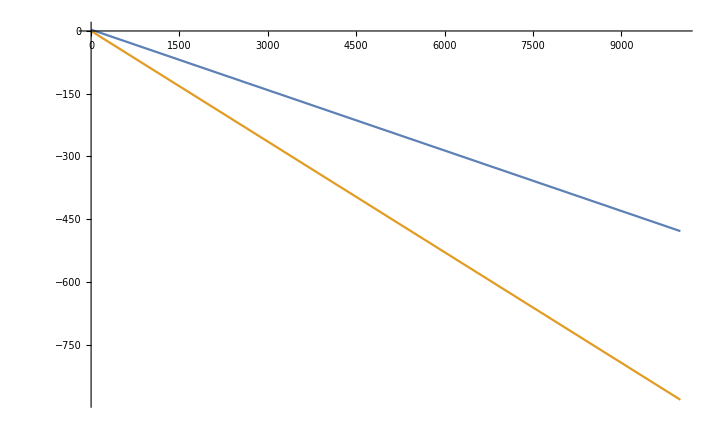

{-0.136357}

{0.0400801}

{-0.0481845}

{-0.0881852}

```mathematica
s1=NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.7,Jy[0]==0.3,ϕx[0]==π,ϕy[0]==0}/.{ν0->0.18,f2->.061,f1->0,R->1,p->0,r->0,δ->-0.02,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}];
Plot[Evaluate[{ϕx[t],ϕy[t]}/.s1,{t,0,10000}]]
(((ϕx[t]/.s1)/.{t->500})-(((ϕx[t]/.s1)/.{t->0})))/500+(((ϕy[t]/.s1)/.{t->500})-(((ϕy[t]/.s1)/.{t->0})))/500
(((ϕx[t]/.s1)/.{t->500})-(((ϕx[t]/.s1)/.{t->0})))/500-(((ϕy[t]/.s1)/.{t->500})-(((ϕy[t]/.s1)/.{t->0})))/500
(((ϕx[t]/.s1)/.{t->50000})-(((ϕx[t]/.s1)/.{t->0})))/50000
(((ϕy[t]/.s1)/.{t->50000})-(((ϕy[t]/.s1)/.{t->0})))/50000
```

```mathematica
Table[ϕx[t]/.Flatten[s1],{t,0,500}];
```

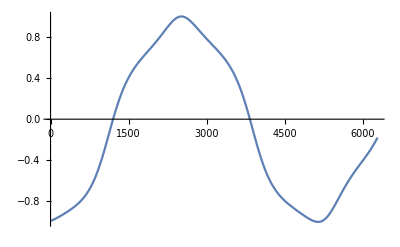

```mathematica
ListPlot[Table[{t,Cos[ϕx[t]]/.Flatten[s1]}/.{t->2 π n},{n,0,1000}],Joined->True]
```

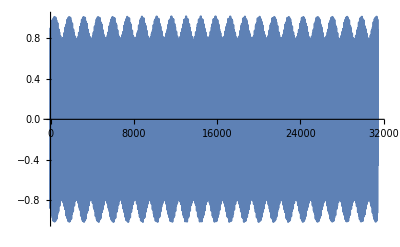

```mathematica
ListPlot[Table[{t,(Sqrt[Jx[t]]Cos[ϕx[t]+.18 t-0.001 t])/.Flatten[s1]}/.{t->2π n},{n,0,5000}],Joined->True]
```

```mathematica
data=Table[{t,(Sqrt[Jx[t]/.Flatten[s1]]Cos[ϕx[t]])/.Flatten[s1]},{t,0,50000}];
(*data1=Table[{t,(Sqrt[Jy[t]]Cos[ϕy[t]])/.Flatten[s1]},{t,0,50000}];
```

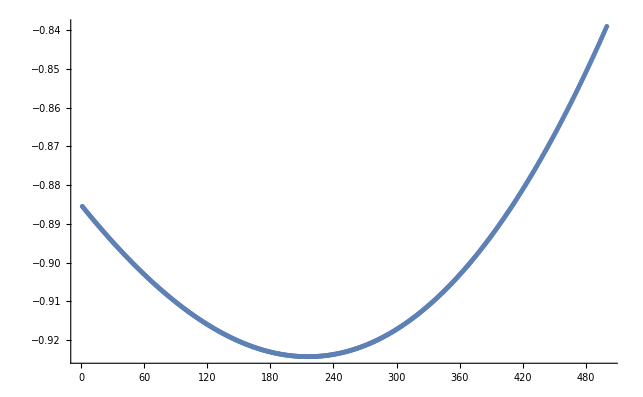

```mathematica
ListPlot[data[[Range[500],2]]]
```

```mathematica
nlm=Abs[Fourier[data[[All,2]]]];
```

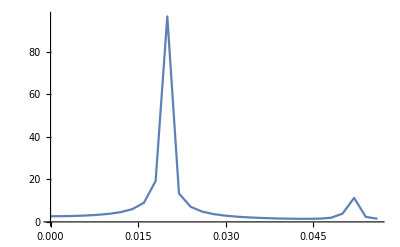

```mathematica
ListPlot[Table[{(n1-1)/(500),nlm[[n1]]},{n1,0,50000}][[Range[0,30]]],PlotRange->All,Joined->True]
```

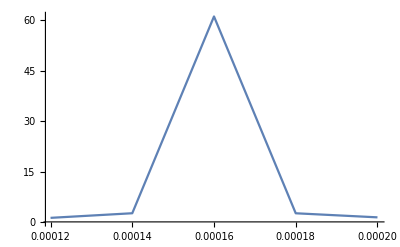

```mathematica
nlm1=Abs[Fourier[data1[[All,2]]]];
ListPlot[Table[{(n1-1)/(50000),nlm1[[n1]]},{n1,0,50000}][[Range[8,12]]],PlotRange->All,Joined->True]
```

```mathematica
listfourierx=Abs[Fourier[Table[Cos[0.171 2 π n],{n,0,10000}]]];
```

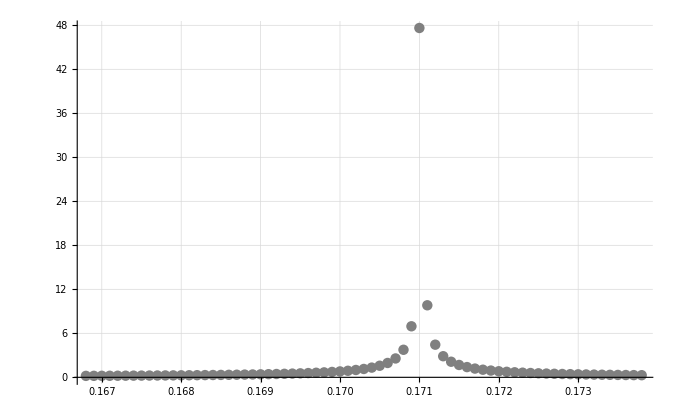

```mathematica
ListPlot[Table[{(n1-1)/(10000),listfourierx[[n1]]},{n1,0,10000}][[Range[1670,1740]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
```

```mathematica
{(ϕx[t]/.Flatten[NDSolve[input/.{Jxv->0.6,Jyv->1-0.6,ϕxv->π,ϕyv->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]])-δ,(ϕy[t]/.Flatten[NDSolve[input/.{Jxv->0.6,Jyv->1-0.6,ϕxv->π,ϕyv->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]])+δ}
```

{-δ+InterpolatingFunction[{{0., 50000.}}, <>][t],δ+InterpolatingFunction[{{0., 50000.}}, <>][t]}

```mathematica
Flatten[NDSolve[(input/.{Jxv->0.6,Jyv->1-0.6,ϕxv->π,ϕyv->0}),{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]]
```

{Jx[t]→InterpolatingFunction[{{0., 50000.}}, <>][t],ϕx[t]→InterpolatingFunction[{{0., 50000.}}, <>][t],Jy[t]→InterpolatingFunction[{{0., 50000.}}, <>][t],ϕy[t]→InterpolatingFunction[{{0., 50000.}}, <>][t]}

```mathematica
Plot[(ϕx[t]/.Flatten[NDSolve[(input/.{Jxv->0.6,Jyv->1-0.6,ϕxv->π,ϕyv->0}),{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]])-δ t,{t,0,1000}]
```

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[0.0204286]==0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],Jy'[0.0204286]==-0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],ϕx'[0.0204286]==-0.04575 (2+Cos[Plus[«3»]]) Jy[0.0204286],ϕy'[0.0204286]==-0.04575 (2+Cos[Plus[«3»]]) Jx[0.0204286],Jx[0]==0.6,Jy[0]==0.4,ϕx[0]==π,ϕy[0]==0},{Jx[0.0204286],ϕx[0.0204286],Jy[0.0204286],ϕy[0.0204286]},{0.0204286,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[0.0204286]==0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],Jy'[0.0204286]==-0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],ϕx'[0.0204286]==-0.04575 (2.+Cos[Plus[«3»]]) Jy[0.0204286],ϕy'[0.0204286]==-0.04575 (2.+Cos[Plus[«3»]]) Jx[0.0204286],Jx[0.]==0.6,Jy[0.]==0.4,ϕx[0.]==3.14159,ϕy[0.]==0.},{Jx[0.0204286],ϕx[0.0204286],Jy[«21»],ϕy[0.0204286]},{0.0204286,0.,50000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 20.4286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{Jx'[20.4286]==0.0915 Jx[20.4286] Jy[20.4286] Sin[1.63429+Times[«2»]+Times[«2»]],Jy'[20.4286]==-0.0915 Jx[20.4286] Jy[20.4286] Sin[1.63429+Times[«2»]+Times[«2»]],ϕx'[20.4286]==-0.04575 (2+Cos[Plus[«3»]]) Jy[20.4286],ϕy'[20.4286]==-0.04575 (2+Cos[Plus[«3»]]) Jx[20.4286],Jx[0]==0.6,Jy[0]==0.4,ϕx[0]==π,ϕy[0]==0},{Jx[20.4286],ϕx[20.4286],Jy[20.4286],ϕy[20.4286]},{20.4286,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
input=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->.061,f1->0,R->1,p->0,r->0,δ->-0.02,s->t});
Manipulate[Manipulate[Manipulate[Manipulate[{Plot[{(ϕx[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}]),(ϕy[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}])},{t,0,1000}],(((ϕx[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}])/.{t->50000})-(((ϕx[t]/.NDSolve[input/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->ϕxv1,ϕyv->ϕyv1},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50000}])/.{t->0})))/50000},{Jxv1,0.2,0.8}],{Jyv1,0.4,0.4}],{ϕxv1,π,π}],{ϕyv1,0,0}]
```

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[0.0204286]==0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],Jy'[0.0204286]==-0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],ϕx'[0.0204286]==-0.04575 (2+Cos[Plus[«3»]]) Jy[0.0204286],ϕy'[0.0204286]==-0.04575 (2+Cos[Plus[«3»]]) Jx[0.0204286],Jx[0]==0.2,Jy[0]==0.8,ϕx[0]==π,ϕy[0]==0},{Jx[0.0204286],ϕx[0.0204286],Jy[0.0204286],ϕy[0.0204286]},{0.0204286,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[0.0204286]==0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],Jy'[0.0204286]==-0.0915 Jx[0.0204286] Jy[0.0204286] Sin[0.00163429+Times[«2»]+Times[«2»]],ϕx'[0.0204286]==-0.04575 (2.+Cos[Plus[«3»]]) Jy[0.0204286],ϕy'[0.0204286]==-0.04575 (2.+Cos[Plus[«3»]]) Jx[0.0204286],Jx[0.]==0.2,Jy[0.]==0.8,ϕx[0.]==3.14159,ϕy[0.]==0.},{Jx[0.0204286],ϕx[0.0204286],Jy[«21»],ϕy[0.0204286]},{0.0204286,0.,50000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 20.4286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{Jx'[20.4286]==0.0915 Jx[20.4286] Jy[20.4286] Sin[1.63429+Times[«2»]+Times[«2»]],Jy'[20.4286]==-0.0915 Jx[20.4286] Jy[20.4286] Sin[1.63429+Times[«2»]+Times[«2»]],ϕx'[20.4286]==-0.04575 (2+Cos[Plus[«3»]]) Jy[20.4286],ϕy'[20.4286]==-0.04575 (2+Cos[Plus[«3»]]) Jx[20.4286],Jx[0]==0.2,Jy[0]==0.8,ϕx[0]==π,ϕy[0]==0},{Jx[20.4286],ϕx[20.4286],Jy[20.4286],ϕy[20.4286]},{20.4286,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

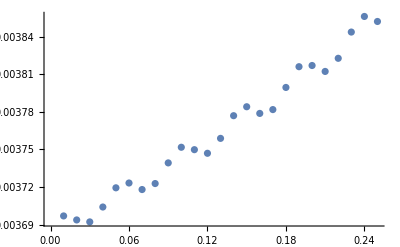

```mathematica
ListPlot[Table[{Jxv1,(((ϕx[t]/.Flatten[NDSolve[input/.{Jxv->Jxv1,Jyv->.25,ϕxv->1,ϕyv->5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕx[t]/.Flatten[NDSolve[input/.{Jxv->Jxv1,Jyv->.25,ϕxv->1,ϕyv->5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.01,0.25,.01}]]
```

```mathematica
Manipulate[ListPlot[Table[{Jxv1,(((ϕy[t]/.Flatten[NDSolve[input/.{Jxv->Jxv1,Jyv->.25,ϕxv->q,ϕyv->5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->5000})-(((ϕy[t]/.Flatten[NDSolve[input/.{Jxv->Jxv1,Jyv->.25,ϕxv->q,ϕyv->5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]])/.{t->0})))/5000},{Jxv1,0.1,0.9,.1}],PlotRange->{0,0.02}],{q,0,2π}]
```

NDSolve::deqn: Equation or list of equations expected instead of input in the first argument input.

ReplaceAll::reps: {NDSolve[input,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 5000 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[input,{Jx[5000],ϕx[5000],Jy[5000],ϕy[5000]},{5000,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of input in the first argument input.

ReplaceAll::reps: {NDSolve[input,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::deqn: Equation or list of equations expected instead of input in the first argument input.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

NDSolve::dsvar: 5000 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
input/.{Jxv->1.4,Jyv->.25,ϕxv->1,ϕyv->5}
```

{Jx'[t]==0.015 Jx[t] Jy[t] Sin[0.04 t+2 ϕx[t]-2 ϕy[t]],Jy'[t]==-0.015 Jx[t] Jy[t] Sin[0.04 t+2 ϕx[t]-2 ϕy[t]],ϕx'[t]==0.0075 (2+Cos[0.04 t+2 ϕx[t]-2 ϕy[t]]) Jy[t],ϕy'[t]==0.0075 (2+Cos[0.04 t+2 ϕx[t]-2 ϕy[t]]) Jx[t],Jx[0]==1.4,Jy[0]==0.25,ϕx[0]==1,ϕy[0]==5}

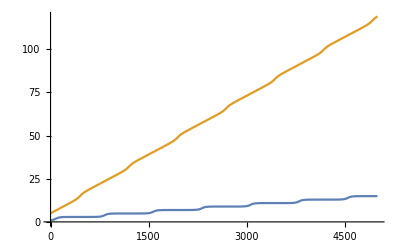

NDSolve::deqn: Equation or list of equations expected instead of input in the first argument input.

ReplaceAll::reps: {NDSolve[input,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[input,{Jx[0.102143],ϕx[0.102143],Jy[0.102143],ϕy[0.102143]},{0.102143,0,5000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[input,{Jx[0.102143],ϕx[0.102143],Jy[0.102143],ϕy[0.102143]},{0.102143,0.,5000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 102.143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
Manipulate[Plot[Evaluate[{ϕx[t],ϕy[t]}/.NDSolve[input/.{Jxv->Jxv1,Jyv->.15,ϕxv->1,ϕyv->5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}],{t,0,5000}]],{Jxv1,1.43,1.44}]
Plot[Evaluate[{ϕx[t],ϕy[t]}/.NDSolve[input/.{Jxv->1.44,Jyv->.25,ϕxv->1,ϕyv->5},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}],{t,0,5000}]]
```

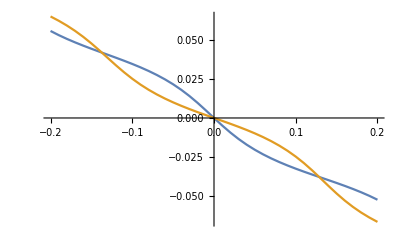

```mathematica
table=Table[{n/100-.2,(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.2, f1->0,R->1,p->0,r->0,δ->-0.001,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.2, f1->0,R->1,p->0,r->0,δ->-0.001,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,40}];
table1=Table[{n/100-.2,(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.2, f1->0,R->1,p->0,r->0,δ->-0.001,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.2, f1->0,R->1,p->0,r->0,δ->-0.001,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,40}];
ListPlot[{table,table1},Joined->True]
```

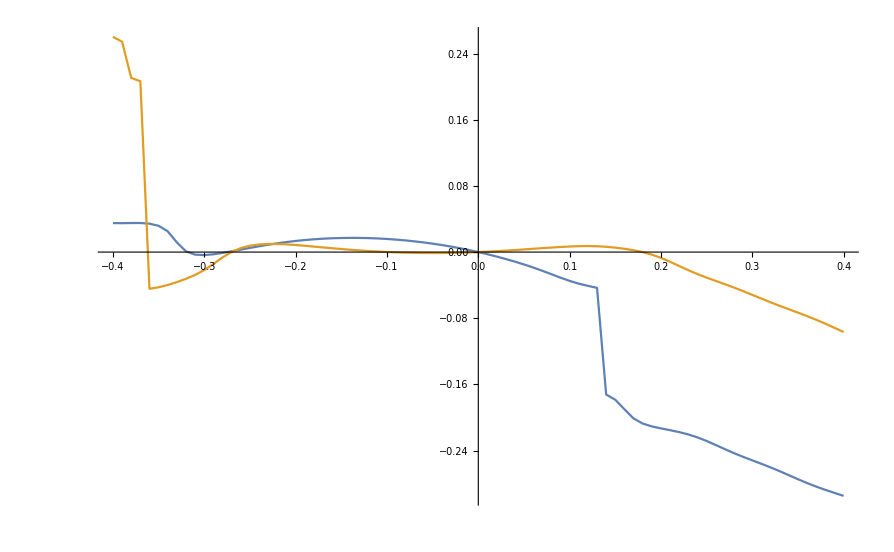

```mathematica
table=Table[{n/100-.4,(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->.1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->.1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,80}];
table1=Table[{n/100-.4,(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->.1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->.1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,80}];
ListPlot[{table,table1},Joined->True]
```

```mathematica
Manipulate[ListPlot[{Table[{n/100-.4,(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->δ1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->δ1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,80}],Table[{n/100-.4,(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->δ1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->n/100-.4, f1->n/100-.4,R->1,p->n/100-.4,r->n/100-.4,δ->δ1,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,80}]},Joined->True],{δ1,-0.1,0.1}]
```

NDSolve::underdet: There are more dependent variables, {J[t],Jx[t],Jy[t],Φ[t],ϕx[t],ϕy[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{Jx'[t]=={0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»],0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»]},Jy'[t]=={-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»],-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»]},ϕx'[t]=={-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»],-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»]},«3»,ϕx[0]==π,ϕy[0]==0},«1»,{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]=={0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»],0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»]},Jy'[50]=={-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»],-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»]},«4»,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::underdet: There are more dependent variables, {J[t],Jx[t],Jy[t],Φ[t],ϕx[t],ϕy[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{Jx'[t]=={0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»],0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»]},Jy'[t]=={-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»],-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»]},ϕx'[t]=={-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»],-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»]},«3»,ϕx[0]==π,ϕy[0]==0},«1»,{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::underdet: There are more dependent variables, {J[t],Jx[t],Jy[t],Φ[t],ϕx[t],ϕy[t]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve::underdet will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
Manipulate[ListPlot[{Table[{n/100-.4,(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->δ1, f1->δ1,R->1,p->δ1,r->δ1,δ->n/100-.4,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕx[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->δ1, f1->δ1,R->1,p->δ1,r->δ1,δ->n/100-.4,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,80}],Table[{n/100-.4,(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->δ1, f1->δ1,R->1,p->δ1,r->δ1,δ->n/100-.4,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->50})-(((ϕy[t]/.Flatten[NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0}/.{II->0.3,f2->δ1, f1->δ1,R->1,p->δ1,r->δ1,δ->n/100-.4,s->t},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]])/.{t->0})))/50},{n,0,80}]},Joined->True],{δ1,-0.4,0.4}]
```

NDSolve::underdet: There are more dependent variables, {J[t],Jx[t],Jy[t],Φ[t],ϕx[t],ϕy[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{Jx'[t]=={0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»],0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»]},Jy'[t]=={-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»],-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»]},ϕx'[t]=={-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»],-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»]},«3»,ϕx[0]==π,ϕy[0]==0},«1»,{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]=={0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»],0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»]},Jy'[50]=={-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»],-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»]},«4»,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::underdet: There are more dependent variables, {J[t],Jx[t],Jy[t],Φ[t],ϕx[t],ϕy[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{Jx'[t]=={0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»],0.2 Power[«2»] Sin[«1»]-0.6 Jx[«1»] Jy[«1»] Sin[«1»]},Jy'[t]=={-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»],-0.2 Power[«2»] Sin[«1»]+0.6 Jx[«1»] Jy[«1»] Sin[«1»]},ϕx'[t]=={-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»],-0.3 Jx[«1»]+0.3 Plus[«2»] Jy[«1»]-0.1 Cos[«1»] Jy[«1»] Power[«2»]},«3»,ϕx[0]==π,ϕy[0]==0},«1»,{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::underdet: There are more dependent variables, {J[t],Jx[t],Jy[t],Φ[t],ϕx[t],ϕy[t]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve::underdet will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 50 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{Jx'[50]==Jxstrd,Jy'[50]==Jystrd,ϕx'[50]==ϕxstrd,ϕy'[50]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[50],ϕx[50],Jy[50],ϕy[50]},{50,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==0.082,Jy[0]==0.218,ϕx[0]==π,ϕy[0]==0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::dsvar: 50 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
_____________---------------------_______without xy_________----------------------__________________
```

```mathematica
h:=δ/R(Ja-Jb)+1/2(p Ja^2+2 q Ja Jb+r Jb^2)-f1 Ja Jb (1+Cos[2ϕa-2ϕb+4 δ/R])
```

```mathematica
FullSimplify[-D[h,ϕa]]
```

-2 f1 Ja Jb Sin[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
FullSimplify[D[h,Ja]]
```

-f1 Jb+Ja p+Jb q+δ/R-f1 Jb Cos[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
FullSimplify[-D[h,ϕb]]
```

2 f1 Ja Jb Sin[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
FullSimplify[D[h,Jb]]
```

-f1 Ja+Ja q+Jb r-δ/R-f1 Ja Cos[(4 δ)/R+2 ϕa-2 ϕb]

```mathematica
hh=FullSimplify[h/.{Ja->(II+J)/2,Jb->(II-J)/2,ϕa->ϕb-(2 δ)/R+Φ}]
```

(2 f1 (-II^2+J^2) R+(II+J) ((II+J) p+2 (II-J) q) R+(II-J)^2 r R+8 J δ+2 f1 (-II^2+J^2) R Cos[2 Φ])/(8 R)

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]
```

f1 (-II^2+J^2) Cos[Φ] Sin[Φ]

```mathematica
Φshtrich=FullSimplify[D[hh,J]]
```

(II (p-r) R+J (2 f1+p-2 q+r) R+4 δ+2 f1 J R Cos[2 Φ])/(4 R)

```mathematica
FullSimplify[D[hh,II]]
```

1/4 (-2 f1 II+J (p-r)+II (p+2 q+r)-2 f1 II Cos[2 Φ])

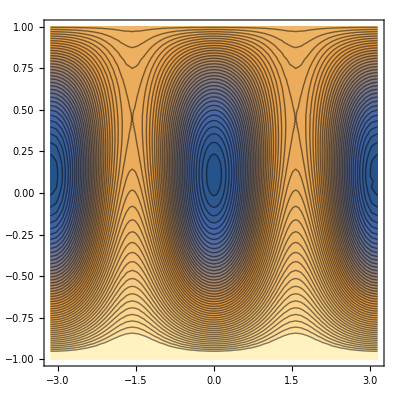

```mathematica
ContourPlot[hh/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},{Φ, -π,π},{J, -1, 1},Contours->50]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[2Φ]->1},J]]
sol1=Flatten[Solve[Φshtrich==0/.{Cos[2Φ]->-1},J]]
```

{J→(-II p R+II r R-4 δ)/((4 f1+p-2 q+r) R)}

{J→(-II p R+II r R-4 δ)/((p-2 q+r) R)}

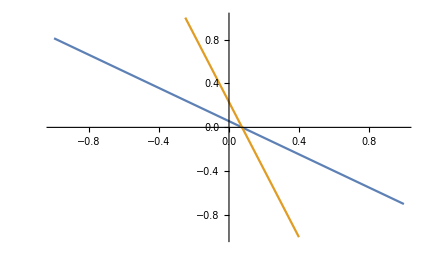

```mathematica
solPlot=sol/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
solPlot1=sol1/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
Jplot={J/.{solPlot[[1]]}};
Jplot1={J/.{solPlot1[[1]]}};
Plot[{Jplot,Jplot1},{δ,-1,1},PlotRange->{-1,1}]
```

```mathematica
Jplot/.{δ->0.075}
```

{0.}

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→0.2/(1.+4 f1)}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→0.64/(0.04+4 f1)}

```mathematica
_____________---------------------_______without p,q, r-------------------__________________
```

```mathematica
hh=Simplify[1/(8 R)(2 f1 (-II^2+J^2) R+8 J δ-4 f √((II-J) (II+J)) R Cos[Φ]+2 f1 (-II^2+J^2) R Cos[2 Φ])]
```

1/4 (f1 (-II^2+J^2)+(4 J δ)/R-2 f √(II^2-J^2) Cos[Φ]+f1 (-II^2+J^2) Cos[2 Φ])

```mathematica
Jshtrich=FullSimplify[-D[hh,Φ]]
```

-1/2 (f √((II-J) (II+J))+2 f1 (II-J) (II+J) Cos[Φ]) Sin[Φ]

```mathematica
Φshtrich=FullSimplify[D[hh,J]]
```

1/2 (f1 J+(2 δ)/R+(f J Cos[Φ])/(√((II-J) (II+J)))+f1 J Cos[2 Φ])

```mathematica
FullSimplify[D[hh,II]]
```

1/2 II Cos[Φ] (-f/(√((II-J) (II+J)))-2 f1 Cos[Φ])

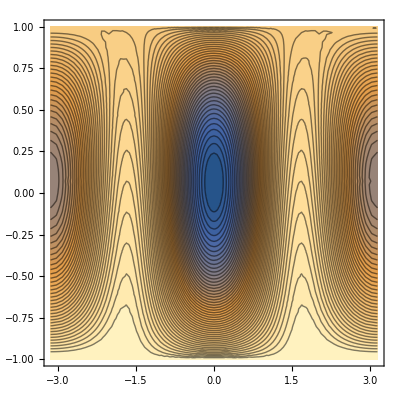

```mathematica
ContourPlot[hh/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6, δ->-0.07},{Φ, -π,π},{J, -1, 1},Contours->50]
```

```mathematica
sol=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-1,Cos[2Φ]->1},δ]]
sol1=Flatten[Solve[Φshtrich==0/.{Cos[Φ]->-f/(2 f1 √(II^2-J^2)),Cos[2Φ]->-1+f^2/(2 f1^2 (II^2-J^2))},δ]]
```

{δ→-((-f J+2 f1 J √(II^2-J^2)) R)/(2 √(II^2-J^2))}

{δ→0}

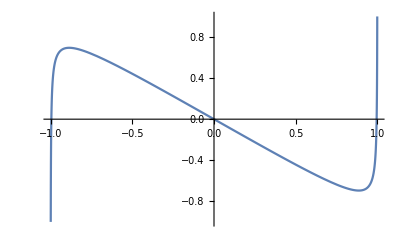

```mathematica
solPlot=sol/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
solPlot1=sol1/.{II->1,f->0.2, f1->1,R->1,p->0.3,q->-.2,r->0.6};
Jplot={δ/.{solPlot[[1]]}};
Plot[{Jplot,Jplot1},{J,-1,1},PlotRange->{-1,1}]
```

```mathematica
Jplot/.{δ->-0.7}
```

{0.584906}

```mathematica
sol1=sol/.{II->1,f->-0.2,δ->-0.04,R->1,p->-0.02,q->-0.5,r->0.02}
```

{J→0.2/(1.+4 f1)}

```mathematica
sol2=sol/.{II->1,f->-0.2,δ->0.09,R->1,p->-0.5,q->-0.02,r->0.5}
```

{J→0.64/(0.04+4 f1)}

```mathematica
►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►
►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►►
```

```mathematica
-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]_Jstr_sum
1/4 (II p-II r+J[t] (2 f1+p-2 q+r)+(4 η Cos[Θ])/R+(2 η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+2 f1 J[t] Cos[2 Φ[t]])_Φstr_sum
f1 (-II^2+J[t]^2) Cos[Φ[t]] Sin[Φ[t]]_Jstr_Without_xy
(II (p-r) R+J[t](2 f1+p-2 q+r) R+4 η Cos[Θ]+2 f1 J[t] R Cos[2 Φ[t]])/(4 R)_Φstr_Without_xy
-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]_Jstr_Without_pqr
1/2 (f1 J[t]+(2 η Cos[Θ])/R+(η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+f1 J[t] Cos[2 Φ[t]])_Φstr_Without_pqr
```

```mathematica
JStr=-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7,f1->1};
ΦStr=1/4 (II p-II r+J[t] (2 f1+p-2 q+r)+(4 η Cos[Θ])/R+(2 η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+2 f1 J[t] Cos[2 Φ[t]])/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7, f1->1};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-

```mathematica
JStr=f1 (-II^2+J[t]^2) Cos[Φ[t]] Sin[Φ[t]]/.{II->1,η->.6,Θ->0,R->1,p->0.3,q->-0.2,r->0.6,f1->1};
ΦStr=(II (p-r) R+J[t](2 f1+p-2 q+r) R+4 η Cos[Θ]+2 f1 J[t] R Cos[2 Φ[t]])/(4 R)/.{II->1,η->.6,Θ->0,R->1,p->0.3,q->-0.2,r->0.6,f1->1};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-

```mathematica
JStr=-1/2 (η Sin[Θ] √((II-J[t]) (II+J[t]))+2 f1 (II-J[t]) (II+J[t]) Cos[Φ[t]]) Sin[Φ[t]]/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7,f1->1};
ΦStr=1/2 (f1 J[t]+(2 η Cos[Θ])/R+(η Sin[Θ] J[t] Cos[Φ[t]])/(√((II-J[t]) (II+J[t])))+f1 J[t] Cos[2 Φ[t]])/.{II->1,η->1,Θ->1.37 ,R->2,p->1.7,q->0,r->1.7, f1->1};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==0.0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.75,Φ[0]==.001+4π/3},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];
Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20},PlotRange->Full]
```

-Graphics3D-